# Faster transport with a directed quantum walk

## Stephan Hoyer

Source code for Fig. 2.
See arXiv:0901.1007 [quant-ph]

```mathematica
Coin[ϕ_]:=Map[Fourier[#]&,ϕ]
Shift[ϕ_]:=Thread[f[ϕ⟦All,2;;Length[ϕ⟦1,All⟧]⟧,RotateRight[ϕ⟦All,1⟧,1]]]/.f:>Prepend
TimeStep[ϕ_]:=Shift[Coin[ϕ]]
Measure[ϕ_]:=Map[Norm[#,2]^2&,ϕ]
DirectedWalk[n_,l_,t_]:=Measure[Nest[TimeStep,PadRight[{UnitVector[n,1]},l,{ConstantArray[0,n]}],t]];
```

```mathematica
qdata=Table[DirectedWalk[n,101,100],{n,2,20}]//N;
cdata=Table[Table[PDF[BinomialDistribution[100,1/n],k],{k,0,100}],{n,2,20}]//N;
```

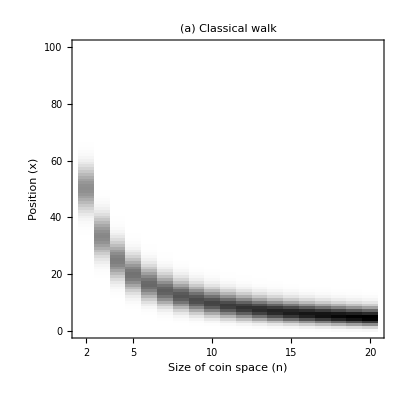

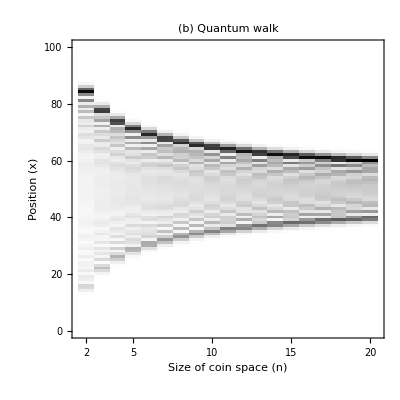

```mathematica
Gc=ArrayPlot[Reverse[Transpose[cdata],1],Frame->{{True,False},{True,False}},AspectRatio->1,PlotRangePadding->None,ClippingStyle->None,FrameLabel->{"Position (x)","Size of coin space (n)"},PlotLabel->"(a) Classical walk",FrameTicks->{{{1,100},{21,80},{41,60},{61,40},{81,20},{101,0}},Join[Thread[{Table[i-1,{i,{2,5,10,15,20}}],Table[j,{j,{2,5,10,15,20}}],Table[0,{i,2,10,2}]}],Table[{i,""},{i,1,20}]]},BaseStyle->{FontSize->10},ImageMargins->None]
Gq=ArrayPlot[Reverse[Transpose[qdata],1],Frame->{{True,False},{True,False}},AspectRatio->1,PlotRangePadding->None,ClippingStyle->None,FrameLabel->{"Position (x)","Size of coin space (n)"},PlotLabel->"(b) Quantum walk",FrameTicks->{{{1,100},{21,80},{41,60},{61,40},{81,20},{101,0}},Join[Thread[{Table[i-1,{i,{2,5,10,15,20}}],Table[j,{j,{2,5,10,15,20}}],Table[0,{i,2,10,2}]}],Table[{i,""},{i,1,20}]]},BaseStyle->{FontSize->10},ImageMargins->None]
```

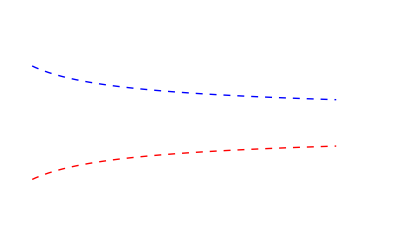

```mathematica
Gqanal=Plot[{100(1-1/(√(n+1+.5)))/2,101(1+1/(√(n+1+.5)))/2},{n,0.5,18.5},PlotRange->{{2,20},{0,100}},Axes->None,PlotStyle->{{Thick,Red,Dashed},{Thick,Blue,Dashed}}]//N
```

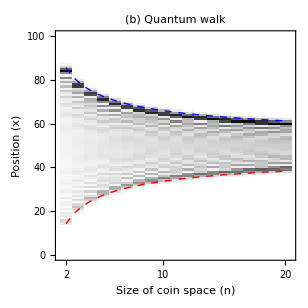

```mathematica
Show[{Gq,Gqanal}]
```

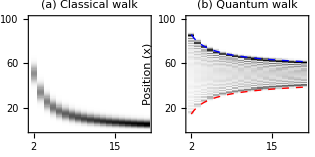

```mathematica
GraphicsRow[{Gc,Show[{Gq,Gqanal}]},0,ImageSize->72 35/8,Frame->None]
```

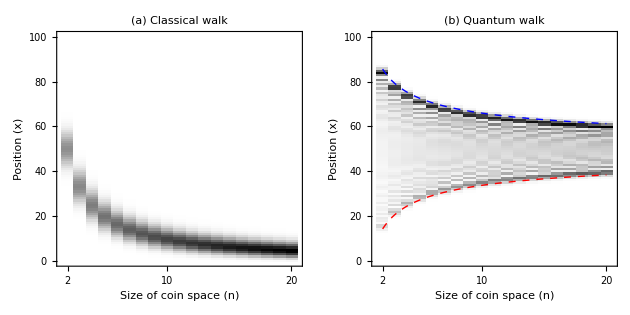

```mathematica
GraphicsRow[{Gc,Show[{Gq,Gqanal}]},0,ImageSize->2 72 35/8,Frame->None]
```

```mathematica
Manipulate[ListPlot[DirectedWalk[n,t,t],Joined->True,PlotRange->{0,.3},AxesLabel->{"x","p"},PlotLabel->"Time evolution for a "<>ToString[n]<>"-dimensional coin after "<>ToString[t]<>" steps"],{n,2,10,1},{t,1,100,1}]
```